# Exercise 3

First define and draw the function

```mathematica
f[x_]:= Sin[x]*1/(E^x)
Simplify[f[x]]
```

ⅇ^-x Sin[x]

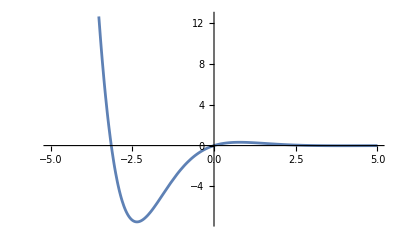

/Users/giulialavizzari/Documents/SciComp_python/Lecture5/ex3.png

```mathematica
myplot=Plot[f[x],{x,-5,5}]
Export["/Users/giulialavizzari/Documents/SciComp_python/Lecture5/ex3.png",myplot]
```

I would like to compute limits before proceeding.

```mathematica
Limit[f[x],x->-∞]
Limit[f[x],x->+∞]
```

Indeterminate

0

Now let’s try and compute the integral

```mathematica
i[x_]=Integrate[f[x],x]
```

-1/2 ⅇ^-x (Cos[x]+Sin[x])

Now let’s try and compute the derivative

```mathematica
D[i[x],x]
Simplify[%]
```

-1/2 ⅇ^-x (Cos[x]-Sin[x])+1/2 ⅇ^-x (Cos[x]+Sin[x])

ⅇ^-x Sin[x]